```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

/home/chenyr/工作区/ModelA_realsystem/grid0_15/exam/buffer

```mathematica
rho=Flatten[Import["rho.dat"]];
V1=Flatten[Import["V1.dat"]];
```

```mathematica
xp=Flatten[Import["xp.dat"]];
eta=Flatten[Import["etapi_k.dat"]];
```

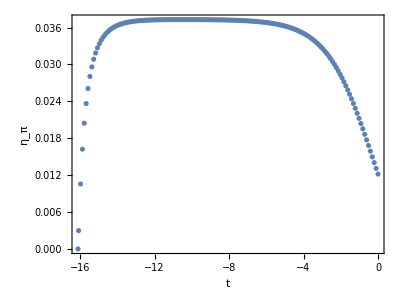

```mathematica
ListPlot[Transpose[{Log[xp/1000],eta}][[1;;-1]],PlotRange->All,AspectRatio->0.75,PlotTheme->"Frame",FrameLabel->{"t","η_π"}]
```

```mathematica
Log[0.005/1000]//N
```

-12.2061

```mathematica
dVdrho1=Interpolation[Transpose[{rho,V1}]]
```

InterpolatingFunction[…]

```mathematica
c0=SetPrecision[Table[c0,{c0,10^-5,10^-3,(10^-3-10^-5)/49}],30];
```

```mathematica
eqn=Table[Evaluate
[(test=SetPrecision[dVdrho1[ρ]-c*(2ρ)^(-1/2),40])]==0,{c,c0}];
```

```mathematica
eqn=Table[Evaluate
[(test=SetPrecision[Sum[list2[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,30}]+1/2 First[list]-c*(2ρ)^(-1/2),40])]==0,{c,c0}];
```

```mathematica
res=Flatten[ParallelMap[FindRoot[#,{ρ,0.00000001},WorkingPrecision->40]&,eqn]][[All,2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 40. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 40. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 40. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 40. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{0.0001423794611680704736756785788236385968547,0.0002990098991652032863841623461059606368819,0.0004212462665719834018176266249047516104118,0.0005276997897741866787836183648252760079237,0.0006243050096693094180780891961340702365369,0.0007139298451701893506313256191304434937976,0.0007982371495072442279616261228892353915468,0.0008782996512856522185098205433753645793742,0.0009548602706050291153387061687697544793736,0.001028460354983950275508127132299522373858,0.001099509779949525416853362302997297796728,0.001168328315616602225858084898165129331843,0.001235171516149356098355053810584051244567,0.001300247698410390392305650829702013560283,0.001363729509430800626516462325467774830191,0.001425762061137533490418178506672933838101,0.001486468806438280787717905374346245981577,0.001545955882403027023246657882018100719444,0.001604315384982981455013879096664252476097,0.001661627881524571000564257039314452584773,0.001717964368373129031984680953031317300643,0.001773387817139742895038244038784025990213,0.001827954411120697509597672918362011504207,0.001881714544929764782176508248388927646493,0.001934713640807788763031282071472443944398,0.001986992821317296970633374940750546347928,0.002038589468313156421302029261755261063438,0.00208953769096840505438530509392049425241,0.002139868720411313845862222157127698333865,0.002189611244645101986415688322355184802007,0.002238791694498909612327261036705577297469,0.002287434489135949734834365919430187555997,0.002335562247937392569995283999415433571318,0.002383195974257024514035038602797036310878,0.002430355215506931229261929923024515205599,0.002477058203218673221425282161733714210006,0.002523321976076792789933178080833772273412,0.002569162488403188849043889941522473194626,0.002614594706153957938498285300245915149359,0.002659632692152325756459900909868220326536,0.002704289682005706530556399494842381094416,0.002748578151929586678255977648259028612081,0.002792509879514531050284410504089525206193,0.002836095998319092158826740044945884908874,0.002879347047042965147486771266414480851771,0.002922273013927931551119440809453436148648,0.002964883376944104156992847268855832926185,0.003007187140243421757558547961303132934239,0.003049192867298225373594625034489383865308,0.003090908711088259612515442738564761254393}

```mathematica
mπ=Sqrt[Sum[list2[[n]]*Cos[n*ArcCos[(2res-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,30}]+1/2 First[list]];
```

```mathematica
Export["cmpi.dat",Transpose[{c0,mπ}]]
```

cmpi.dat

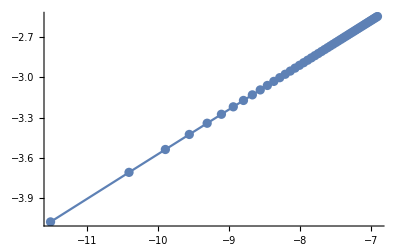

```mathematica
ListLinePlot[data=Transpose[{Log[c0],Log[Sqrt[res*2]]}][[1;;-1]],Mesh->All]
```

```mathematica
Fit[data,{1,x},x]
```

-0.23708765770099942240720717385+0.33376310850125082841772144403 x

```mathematica
x=Table[Log[c/c0],{c,10^-2.325,10^-1.358,(10^-1.358-10^-2.325)/35}];
y=-1.0604063818154787+0.2057021953953145 x;
data2=Transpose[{x,y}];
```

```mathematica
Export["deltabeyond.dat",data2]
```

deltabeyond.dat